## Function declarations (just evaluate and treat as black box for now)

```mathematica
Λ2=1000;
gn=Table[{n,SquaresR[3,n]},{n,0,Λ2}];
```

```mathematica
X1[nn_,s_,η_]:=Module[{answer,deg,j2,exp},
answer=0;
Do[
j2=gn[[n,1]];
If[j2≠ nn,
deg=gn[[n,2]];
exp=Exp[-η (j2-nn)]/(j2-nn)^s;
Do[answer += deg (η (j2-nn))^i/(i!)exp,
{i,0,s-1}]],
{n,1,Λ2}
];
Return[answer];
];
```

```mathematica
X2[nn_,s_,η_]:=Module[{answer,deg},
answer=0;
If[Mod[nn,1]==0&& nn≥0,
deg=gn[[nn+1,2]],
deg=0
];
If[s==1,
Return[4 π Integrate[-Exp[-η (y^2-nn)]+nn (1-Exp[-η (y^2-nn)])/(y^2-nn),{y,0,Infinity},PrincipalValue->True]-deg η],
Return[Integrate[4 π y^2/((y^2-nn)^s)(1-Exp[-η (y^2-nn)]Sum[((η (y^2-nn))^n)/(n!),{n,0,s-1}]),{y,0,Infinity},PrincipalValue->True]-deg η^s/(s!)]];
];
```

```mathematica
Iα1[n_,α_,η_,prec_]:=N[X1[n,α,η],prec]+N[X2[n,α,η],prec];
Z[q2_]:=1/(2 √π)Iα1[q2,α=1,η=1/10,prec=15];
```

## What you just evaluated above

Hi Christopher--the functions you evaluated above are my routines for calculating Lüscher’s formula.  They are based off the method described in Appendix C of [arXiv:0709.2530] (paper by S. Tan).  The overall routine is slow (sorry), but is good to the 15^th decimal point.  The routine  that calculates S_3is called with

Z[(q̃)^2]

where

(q̃)^2=(qL/(2 π))^2

The relationship to the scattering phase shift (as defined in my paper with Savage) is

L qcotδ[q] = 2/π^(1/2)Z[(q̃)^2]

or equivalently

q̃ cotδ[q] = 1/π^(3/2)Z[(q̃)^2]

Also, one more thing :  As you know, Lüscher' s formula has poles at the non-interacting energies ((q̃)^2=0,1,2,etc.).  However, my routine above will evaluate to a finite value at any of these poles.  These finite values are the residues at these poles (which are useful in perturbation theory).

### Data (just evaluate)

I evaluated my routine for a bunch of values:  I store them here:

```mathematica
zdat={{-4.,-11.136637304797215},{-3.99,-11.12270747635899},{-3.98,-11.10876017629406},{-3.97,-11.094795338637264},{-3.96,-11.080812897006435},{-3.95,-11.06681278459875},{-3.94,-11.052794934186911},{-3.93,-11.038759278115396},{-3.92,-11.024705748296594},{-3.91,-11.010634276206932},{-3.9,-10.996544792882908},{-3.89,-10.982437228917153},{-3.88,-10.968311514454395},{-3.87,-10.954167579187363},{-3.86,-10.940005352352687},{-3.85,-10.925824762726744},{-3.84,-10.911625738621408},{-3.83,-10.897408207879776},{-3.82,-10.883172097871903},{-3.81,-10.86891733549036},{-3.8,-10.85464384714585},{-3.79,-10.840351558762745},{-3.78,-10.826040395774529},{-3.77,-10.811710283119176},{-3.76,-10.797361145234602},{-3.75,-10.782992906053922},{-3.74,-10.768605489000635},{-3.73,-10.754198816983926},{-3.7199999999999998,-10.739772812393687},{-3.71,-10.72532739709566},{-3.7,-10.7108624924264},{-3.69,-10.696378019188263},{-3.68,-10.681873897644238},{-3.67,-10.667350047512809},{-3.66,-10.652806387962679},{-3.65,-10.638242837607482},{-3.64,-10.623659314500415},{-3.63,-10.609055736128745},{-3.62,-10.594432019408362},{-3.61,-10.57978808067811},{-3.6,-10.565123835694244},{-3.59,-10.550439199624591},{-3.58,-10.535734087042846},{-3.57,-10.521008411922633},{-3.56,-10.506262087631596},{-3.55,-10.49149502692533},{-3.54,-10.47670714194134},{-3.53,-10.461898344192816},{-3.52,-10.44706854456237},{-3.51,-10.432217653295695},{-3.5,-10.417345579995178},{-3.49,-10.402452233613328},{-3.48,-10.387537522446209},{-3.4699999999999998,-10.372601354126783},{-3.46,-10.357643635618066},{-3.45,-10.342664273206353},{-3.44,-10.327663172494182},{-3.4299999999999997,-10.312640238393362},{-3.42,-10.297595375117773},{-3.41,-10.282528486176169},{-3.4,-10.26743947436482},{-3.39,-10.25232824176008},{-3.38,-10.23719468971089},{-3.37,-10.222038718831065},{-3.36,-10.206860228991644},{-3.35,-10.191659119312984},{-3.34,-10.176435288156785},{-3.33,-10.161188633118106},{-3.32,-10.145919051017122},{-3.31,-10.130626437890841},{-3.3,-10.11531068898475},{-3.29,-10.09997169874422},{-3.2800000000000002,-10.084609360805894},{-3.27,-10.069223567988978},{-3.26,-10.053814212286232},{-3.25,-10.038381184855115},{-3.24,-10.022924376008472},{-3.23,-10.007443675205414},{-3.2199999999999998,-9.991938971041828},{-3.21,-9.976410151240845},{-3.2,-9.960857102643205},{-3.19,-9.945279711197413},{-3.1799999999999997,-9.929677861949768},{-3.17,-9.914051439034298},{-3.16,-9.898400325662482},{-3.15,-9.882724404112833},{-3.14,-9.867023555720431},{-3.13,-9.851297660866088},{-3.12,-9.835546598965598},{-3.11,-9.81977024845861},{-3.1,-9.803968486797514},{-3.09,-9.788141190436049},{-3.08,-9.772288234817772},{-3.07,-9.756409494364346},{-3.06,-9.740504842463684},{-3.05,-9.72457415145785},{-3.04,-9.70861729263088},{-3.0300000000000002,-9.692634136196272},{-3.02,-9.676624551284409},{-3.01,-9.660588405929742},{-3.,-9.64452556705776},{-2.99,-9.62843590047179},{-2.98,-9.61231927083956},{-2.9699999999999998,-9.596175541679573},{-2.96,-9.58000457534727},{-2.95,-9.563806233020957},{-2.94,-9.547580374687538},{-2.9299999999999997,-9.531326859127974},{-2.92,-9.515045543902556},{-2.91,-9.498736285335942},{-2.9,-9.482398938501904},{-2.8899999999999997,-9.466033357207927},{-2.88,-9.449639393979403},{-2.87,-9.433216900043766},{-2.86,-9.416765725314178},{-2.8499999999999996,-9.400285718373107},{-2.84,-9.383776726455508},{-2.83,-9.367238595431816},{-2.8200000000000003,-9.350671169790616},{-2.81,-9.334074292621027},{-2.8,-9.317447805594812},{-2.79,-9.300791548948183},{-2.7800000000000002,-9.284105361463245},{-2.77,-9.267389080449252},{-2.76,-9.2506425417234},{-2.75,-9.233865579591399},{-2.74,-9.21705802682768},{-2.73,-9.200219714655214},{-2.7199999999999998,-9.183350472725099},{-2.71,-9.166450129095644},{-2.7,-9.149518510211232},{-2.69,-9.132555440880719},{-2.6799999999999997,-9.115560744255502},{-2.67,-9.098534241807188},{-2.66,-9.081475753304842},{-2.65,-9.064385096791865},{-2.6399999999999997,-9.047262088562496},{-2.63,-9.03010654313779},{-2.62,-9.012918273241235},{-2.61,-8.99569708977397},{-2.5999999999999996,-8.978442801789408},{-2.59,-8.961155216467587},{-2.58,-8.943834139088908},{-2.5700000000000003,-8.926479373007435},{-2.56,-8.909090719623702},{-2.55,-8.891667978357058},{-2.54,-8.874210946617431},{-2.5300000000000002,-8.85671941977658},{-2.52,-8.839193191138863},{-2.51,-8.82163205191136},{-2.5,-8.804035791173531},{-2.49,-8.78640419584619},{-2.48,-8.768737050659995},{-2.4699999999999998,-8.751034138123233},{-2.46,-8.733295238489088},{-2.45,-8.715520129722135},{-2.44,-8.697708587464334},{-2.4299999999999997,-8.679860385000236},{-2.42,-8.661975293221584},{-2.41,-8.644053080591174},{-2.4,-8.626093513105996},{-2.3899999999999997,-8.608096354259677},{-2.38,-8.590061365004113},{-2.37,-8.571988303710409},{-2.36,-8.553876926128908},{-2.3499999999999996,-8.535726985348552},{-2.34,-8.51753823175528},{-2.33,-8.49931041298966},{-2.3200000000000003,-8.481043273903607},{-2.31,-8.462736556516202},{-2.3,-8.444389999968612},{-2.29,-8.42600334047802},{-2.2800000000000002,-8.407576311290649},{-2.27,-8.38910864263371},{-2.26,-8.370600061666424},{-2.25,-8.352050292429917},{-2.24,-8.333459055796023},{-2.23,-8.314826069415076},{-2.2199999999999998,-8.296151047662482},{-2.21,-8.277433701584147},{-2.2,-8.258673738840724},{-2.19,-8.23987086365058},{-2.1799999999999997,-8.22102477673157},{-2.17,-8.202135175241406},{-2.16,-8.183201752716828},{-2.15,-8.164224199011228},{-2.1399999999999997,-8.145202200231031},{-2.13,-8.1261354386705},{-2.12,-8.107023592745087},{-2.11,-8.08786633692325},{-2.0999999999999996,-8.068663341656682},{-2.09,-8.049414273308914},{-2.08,-8.030118794082197},{-2.0700000000000003,-8.010776561942754},{-2.06,-7.991387230544153},{-2.05,-7.971950449148913},{-2.04,-7.952465862548169},{-2.0300000000000002,-7.932933110979498},{-2.02,-7.913351830042606},{-2.01,-7.893721650613066},{-2.,-7.8740421987538936},{-1.9899999999999998,-7.854313095624905},{-1.98,-7.834533957389838},{-1.9699999999999998,-7.814704395121197},{-1.96,-7.7948240147026135},{-1.9500000000000002,-7.774892416728766},{-1.94,-7.75490919640276},{-1.9300000000000002,-7.734873943430857},{-1.92,-7.714786241914471},{-1.9100000000000001,-7.694645670239374},{-1.9,-7.674451800962015},{-1.8900000000000001,-7.6542042006928},{-1.88,-7.633902429976306},{-1.87,-7.61354604316831},{-1.8599999999999999,-7.5931345883094785},{-1.85,-7.5726676069957},{-1.8399999999999999,-7.552144634244816},{-1.83,-7.531565198359767},{-1.8199999999999998,-7.51092882078794},{-1.81,-7.490235015976588},{-1.7999999999999998,-7.469483291224265},{-1.79,-7.4486731465280345},{-1.7799999999999998,-7.427804074426362},{-1.77,-7.406875559837548},{-1.7599999999999998,-7.385887079893511},{-1.75,-7.364838103768731},{-1.7399999999999998,-7.343728092504291},{-1.73,-7.322556498826674},{-1.7199999999999998,-7.301322766961268},{-1.71,-7.2800263324403},{-1.6999999999999997,-7.258666621905032},{-1.69,-7.237243052902005},{-1.6800000000000002,-7.215755033673043},{-1.67,-7.19420196293887},{-1.6600000000000001,-7.172583229676067},{-1.65,-7.150898212887082},{-1.6400000000000001,-7.129146281363048},{-1.63,-7.10732679343911},{-1.62,-7.085439096742055},{-1.6099999999999999,-7.063482527929748},{-1.6,-7.041456412422308},{-1.5899999999999999,-7.019360064124422},{-1.58,-6.997192785138686},{-1.5699999999999998,-6.974953865469386},{-1.56,-6.952642582716513},{-1.5499999999999998,-6.9302582017594805},{-1.54,-6.9077999744302},{-1.5299999999999998,-6.885267139174983},{-1.52,-6.862658920704864},{-1.5099999999999998,-6.839974529633876},{-1.5,-6.8172131621046494},{-1.4899999999999998,-6.794373999400801},{-1.48,-6.771456207545838},{-1.4699999999999998,-6.748458936887378},{-1.46,-6.725381321666669},{-1.4499999999999997,-6.702222479572328},{-1.44,-6.678981511277792},{-1.4300000000000002,-6.655657499961656},{-1.42,-6.6322495108101105},{-1.4100000000000001,-6.608756590500776},{-1.4,-6.585177766666864},{-1.3900000000000001,-6.561512047340914},{-1.38,-6.537758420377058},{-1.37,-6.513915852850767},{-1.3599999999999999,-6.48998329043516},{-1.35,-6.465959656752407},{-1.3399999999999999,-6.44184385269945},{-1.33,-6.41763475574631},{-1.3199999999999998,-6.393331219206009},{-1.31,-6.368932071474399},{-1.2999999999999998,-6.344436115238574},{-1.29,-6.319842126652074},{-1.2799999999999998,-6.295148854475402},{-1.27,-6.270355019179715},{-1.2599999999999998,-6.245459312012148},{-1.25,-6.22046039402036},{-1.2399999999999998,-6.195356895034495},{-1.23,-6.1701474126038764},{-1.2199999999999998,-6.144830510886245},{-1.21,-6.119404719486882},{-1.1999999999999997,-6.093868532244708},{-1.19,-6.068220405962535},{-1.1800000000000002,-6.04245875907824},{-1.17,-6.016581970273504},{-1.1600000000000001,-5.990588377016462},{-1.15,-5.964476274034591},{-1.1400000000000001,-5.938243911713507},{-1.13,-5.911889494417346},{-1.12,-5.885411178726255},{-1.1099999999999999,-5.8588070715855025},{-1.1,-5.832075228361343},{-1.0899999999999999,-5.805213650797464},{-1.08,-5.778220284865999},{-1.0699999999999998,-5.751093018506339},{-1.06,-5.723829679244912},{-1.0499999999999998,-5.696428031687729},{-1.04,-5.668885774877916},{-1.0299999999999998,-5.641200539509116},{-1.02,-5.613369884985204},{-1.0099999999999998,-5.58539129631606},{-1.,-5.557262180838151},{-0.9899999999999998,-5.5289798647480595},{-0.98,-5.500541589435864},{-0.9699999999999998,-5.471944507604291},{-0.96,-5.443185679158542},{-0.9499999999999997,-5.4142620668503},{-0.94,-5.385170531658033},{-0.9299999999999997,-5.355907827884244},{-0.9199999999999999,-5.326470597948686},{-0.9100000000000001,-5.296855366854592},{-0.8999999999999999,-5.267058536303132},{-0.8900000000000001,-5.2370763784290455},{-0.8799999999999999,-5.20690502912778},{-0.8700000000000001,-5.1765404809421005},{-0.8599999999999999,-5.1459785754728955},{-0.8500000000000001,-5.115214995275816},{-0.8399999999999999,-5.084245255201434},{-0.8300000000000001,-5.053064693133182},{-0.8199999999999998,-5.021668460072082},{-0.81,-4.990051509513063},{-0.7999999999999998,-4.95820858605164},{-0.79,-4.926134213153683},{-0.7799999999999998,-4.893822680014539},{-0.77,-4.8612680274254725},{-0.7599999999999998,-4.828464032557356},{-0.75,-4.79540419256189},{-0.7399999999999998,-4.76208170687948},{-0.73,-4.728489458131596},{-0.7199999999999998,-4.69461999146104},{-0.71,-4.6604654921689965},{-0.6999999999999997,-4.626017761480008},{-0.69,-4.591268190246809},{-0.6799999999999997,-4.556207730384701},{-0.6699999999999999,-4.520826863800367},{-0.6600000000000001,-4.485115568551557},{-0.6499999999999999,-4.449063281941196},{-0.6400000000000001,-4.4126588602137815},{-0.6299999999999999,-4.375890534478303},{-0.6200000000000001,-4.338745862434874},{-0.6099999999999999,-4.301211675426066},{-0.6000000000000001,-4.263274020270781},{-0.5899999999999999,-4.224918095264779},{-0.5800000000000001,-4.186128179647368},{-0.5699999999999998,-4.1468875557354625},{-0.56,-4.107178422812576},{-0.5499999999999998,-4.066981801727414},{-0.54,-4.026277429002525},{-0.5299999999999998,-3.985043639072101},{-0.52,-3.9432572330564355},{-0.5099999999999998,-3.9008933322304644},{-0.5,-3.8579252140496054},{-0.48999999999999977,-3.8143241282477183},{-0.48,-3.7700590901074955},{-0.46999999999999975,-3.725096647511204},{-0.45999999999999996,-3.679400617789737},{-0.44999999999999973,-3.6329317896803555},{-0.43999999999999995,-3.5856475848517615},{-0.4299999999999997,-3.5375016724241175},{-0.41999999999999993,-3.4884435286610005},{-0.41000000000000014,-3.438417932483661},{-0.3999999999999999,-3.3873643855894495},{-0.3900000000000001,-3.3352164436552774},{-0.3799999999999999,-3.2819009422619794},{-0.3700000000000001,-3.227337097637967},{-0.3599999999999999,-3.171435457898905},{-0.3500000000000001,-3.1140966749017918},{-0.33999999999999986,-3.0552100598015968},{-0.33000000000000007,-2.994651876452201},{-0.31999999999999984,-2.9322833153291077},{-0.31000000000000005,-2.8679480758616087},{-0.2999999999999998,-2.801469465831968},{-0.29000000000000004,-2.7326469013047143},{-0.2799999999999998,-2.6612516572539193},{-0.27,-2.5870216746645314},{-0.2599999999999998,-2.5096551701246193},{-0.25,-2.428802712654217},{-0.23999999999999977,-2.344057320767588},{-0.22999999999999998,-2.2549419772904122},{-0.21999999999999975,-2.1608937403737514},{-0.20999999999999996,-2.0612433161772685},{-0.19999999999999973,-1.95518850488734},{-0.18999999999999995,-1.8417592629698205},{-0.17999999999999972,-1.7197711214075455},{-0.16999999999999993,-1.5877621654450549},{-0.16000000000000014,-1.4439063841322508},{-0.1499999999999999,-1.2858923623913185},{-0.14000000000000012,-1.1107499870414874},{-0.1299999999999999,-0.9145971744967007},{-0.1200000000000001,-0.6922599663437664},{-0.10999999999999988,-0.43668540899464303},{-0.10000000000000009,-0.13800216658385372},{-0.08999999999999986,0.2180451177632882},{-0.08000000000000007,0.6528356820090013},{-0.06999999999999984,1.1999609474117368},{-0.06000000000000005,1.9154011113115015},{-0.04999999999999982,2.8999136363908686},{-0.040000000000000036,4.355004454017153},{-0.029999999999999805,6.750841546101254},{-0.020000000000000018,11.497909227435684},{-0.009999999999999787,25.64858802574905},{0.,-2.514489421834971},{0.009999999999999787,-30.677092805361216},{0.020000000000000462,-16.524991379601794},{0.03000000000000025,-11.775551200376096},{0.040000000000000036,-9.376389557384378},{0.04999999999999982,-7.917019071514397},{0.0600000000000005,-6.927267806007979},{0.07000000000000028,-6.2056249727521635},{0.08000000000000007,-5.651327336394223},{0.08999999999999986,-5.208387994238671},{0.09999999999999964,-4.843207867396148},{0.11000000000000032,-4.53439908546556},{0.1200000000000001,-4.267696658721608},{0.1299999999999999,-4.033218589211296},{0.13999999999999968,-3.823900199806268},{0.15000000000000036,-3.634554711300957},{0.16000000000000014,-3.461286082466398},{0.16999999999999993,-3.3011090619873866},{0.17999999999999972,-3.151695868205787},{0.1900000000000004,-3.0112028425738857},{0.20000000000000018,-2.878149084195289},{0.20999999999999996,-2.7513297365117046},{0.21999999999999975,-2.6297528984409038},{0.23000000000000043,-2.5125929677917083},{0.2400000000000002,-2.3991556219600323},{0.25,-2.2888511750792206},{0.2599999999999998,-2.181174053881376},{0.27000000000000046,-2.0756868032207114},{0.28000000000000025,-1.9720074859326178},{0.29000000000000004,-1.86979965458055},{0.2999999999999998,-1.7687642916179527},{0.3100000000000005,-1.6686332698500028},{0.3200000000000003,-1.5691639966965016},{0.33000000000000007,-1.4701349868773936},{0.33999999999999986,-1.3713421677308448},{0.35000000000000053,-1.2725957655715099},{0.3600000000000003,-1.1737176545692836},{0.3700000000000001,-1.0745390745713503},{0.3799999999999999,-0.9748986432294688},{0.3899999999999997,-0.8746406022526062},{0.40000000000000036,-0.7736132486864402},{0.41000000000000014,-0.671667510627987},{0.41999999999999993,-0.5686556333042531},{0.4299999999999997,-0.4644299464143245},{0.4400000000000004,-0.35884168737164274},{0.4500000000000002,-0.25173985782625524},{0.45999999999999996,-0.1429700927640422},{0.46999999999999975,-0.03237352269540207},{0.4800000000000004,0.08021438995681222},{0.4900000000000002,0.19496505913291073},{0.5,0.31205804745212046},{0.5099999999999998,0.4316824230068623},{0.5200000000000005,0.5540382227037695},{0.5300000000000002,0.6793380464703934},{0.54,0.8078088095951717},{0.5499999999999998,0.9396936842173897},{0.5600000000000005,1.075254265683769},{0.5700000000000003,1.2147730053212908},{0.5800000000000001,1.3585559583883933},{0.5899999999999999,1.5069359048713575},{0.6000000000000005,1.6602759117951424},{0.6100000000000003,1.8189734193386486},{0.6200000000000001,1.9834649499608596},{0.6299999999999999,2.1542315608343148},{0.6399999999999997,2.3318051862973435},{0.6500000000000004,2.5167760502876453},{0.6600000000000001,2.7098013708139996},{0.6699999999999999,2.911615632128314},{0.6799999999999997,3.123042768976056},{0.6900000000000004,3.3450106959926234},{0.7000000000000002,3.5785687306335734},{0.71,3.8249086091586726},{0.7199999999999998,4.0853899949150065},{0.7300000000000004,4.361571644485547},{0.7400000000000002,4.655249755788914},{0.75,4.968505509821017},{0.7599999999999998,5.303764488191492},{0.7700000000000005,5.663871581442625},{0.7800000000000002,6.052186317590353},{0.79,6.472705418130321},{0.7999999999999998,6.930222111568766},{0.8100000000000005,7.43053574712261},{0.8200000000000003,7.980731270112542},{0.8300000000000001,8.589557325926123},{0.8399999999999999,9.267946142795859},{0.8500000000000005,10.029741357031282},{0.8600000000000003,10.892737752068014},{0.8700000000000001,11.880200864999725},{0.8799999999999999,13.0231463832947},{0.8899999999999997,14.36386283446461},{0.9000000000000004,15.961547873581386},{0.9100000000000001,17.901702077791935},{0.9199999999999999,20.312568066028906},{0.9299999999999997,23.395660268496997},{0.9400000000000004,27.486824436479957},{0.9500000000000002,33.190568527703185},{0.96,41.71588987272918},{0.9699999999999998,55.88375660880028},{0.9800000000000004,84.15703331271614},{0.9900000000000002,168.8499602159127},{1.,-0.3417114862988118},{1.0099999999999998,-169.53264632826964},{1.0200000000000005,-84.83750807835384},{1.0300000000000002,-56.56054324102336},{1.04,-42.38750774360067},{1.0499999999999998,-33.85553161574052},{1.0600000000000005,-28.14363975839869},{1.0700000000000003,-24.042826290320768},{1.08,-20.948573088735746},{1.0899999999999999,-18.525022592537496},{1.1000000000000005,-16.57064688135323},{1.1100000000000003,-14.957188124824748},{1.12,-13.599128766625507},{1.13,-12.437252352399593},{1.1399999999999997,-11.429249676727459},{1.1500000000000004,-10.544082430572246},{1.1600000000000001,-9.758460439659679},{1.17,-9.054562188451255},{1.1799999999999997,-8.418515126447573},{1.1900000000000004,-7.839355833564566},{1.2000000000000002,-7.308302090298647},{1.21,-6.818232880628968},{1.2199999999999998,-6.363310163252008},{1.2300000000000004,-5.938699260049719},{1.2400000000000002,-5.540359093965928},{1.25,-5.1648827137101065},{1.2599999999999998,-4.809374561469453},{1.2700000000000005,-4.471354952257655},{1.2800000000000002,-4.148684956198235},{1.29,-3.839506752671108},{1.2999999999999998,-3.5421958395159345},{1.3100000000000005,-3.255322413101462},{1.3200000000000003,-2.9776199052923378},{1.33,-2.7079591506708653},{1.3399999999999999,-2.4453270155804128},{1.3500000000000005,-2.188808586518888},{1.3600000000000003,-1.9375722147324603},{1.37,-1.6908568645257385},{1.38,-1.4479613275948384},{1.3899999999999997,-1.2082349537703398},{1.4000000000000004,-0.9710696165706579},{1.4100000000000001,-0.7358926847668138},{1.42,-0.5021608123198643},{1.4299999999999997,-0.26935439122468624},{1.4400000000000004,-0.036972536956069287},{1.4500000000000002,0.1954715041542337},{1.46,0.42845462106535037},{1.4699999999999998,0.6624478615226294},{1.4800000000000004,0.8979202880552155},{1.4900000000000002,1.135342735468787},{1.5,1.3751915348538273},{1.5099999999999998,1.6179522671277125},{1.5200000000000005,1.8641236089831872},{1.5300000000000002,2.114221335787464},{1.54,2.3687825495124804},{1.5499999999999998,2.6283702053071982},{1.5600000000000005,2.893578018063523},{1.5700000000000003,3.1650358406011327},{1.58,3.443415618342481},{1.5899999999999999,3.7294380421613686},{1.6000000000000005,4.023880042243207},{1.6100000000000003,4.327583292313778},{1.62,4.641463926807279},{1.63,4.966523715193138},{1.6399999999999997,5.303862990055858},{1.6500000000000004,5.654695691631384},{1.6600000000000001,6.020366975349941},{1.67,6.402373935855781},{1.6799999999999997,6.802390138146372},{1.6900000000000004,7.222294823632489},{1.7000000000000002,7.664207889366991},{1.71,8.130532040783168},{1.7199999999999998,8.6240039175873},{1.7300000000000004,9.147756524959128},{1.7400000000000002,9.705396019140327},{1.75,10.301096871596087},{1.7599999999999998,10.93972077677288},{1.7700000000000005,11.62696653406122},{1.7800000000000002,12.369560763409304},{1.79,13.175503069572969},{1.7999999999999998,14.054384715566721},{1.8100000000000005,15.01780789099776},{1.8200000000000003,16.079944698678563},{1.83,17.258293393578317},{1.8399999999999999,18.574718174871013},{1.8500000000000005,20.056904858593906},{1.8600000000000003,21.740440373843732},{1.87,23.67185199001812},{1.88,25.913166120651848},{1.8899999999999997,28.548953709505966},{1.9000000000000004,31.6976028088001},{1.9100000000000001,35.53010616796498},{1.92,40.30293946936805},{1.9299999999999997,46.4191208602043},{1.9400000000000004,54.550329961662136},{1.9500000000000002,65.90556962582842},{1.96,82.90282025126852},{1.9699999999999998,111.18400263006417},{1.9800000000000004,167.67482918943216},{1.9900000000000002,337.0037623941767},{2.,-1.4377146662149287},{2.01,-339.8789516998043},{2.0200000000000005,-170.5492982599721},{2.0300000000000002,-114.05727079282025},{2.04,-85.77440605807394},{2.05,-68.77499053996112},{2.0600000000000005,-57.417102041770136},{2.0700000000000003,-49.28275844041831},{2.08,-43.16295483468698},{2.09,-38.38600922401326},{2.1000000000000005,-34.5489007449924},{2.1100000000000003,-31.395150654637426},{2.12,-28.753762789876504},{2.13,-26.506345322140778},{2.1400000000000006,-24.568323157780892},{2.1500000000000004,-22.877665347804943},{2.16,-21.38783968848175},{2.17,-20.063253902843773},{2.1799999999999997,-18.876216397337434},{2.1900000000000004,-17.804856747971062},{2.2,-16.831670008340602},{2.21,-15.942476896478942},{2.2199999999999998,-15.12566753287773},{2.2300000000000004,-14.371642428765838},{2.24,-13.672393190412933},{2.25,-13.02118381586854},{2.26,-12.41230549824258},{2.2700000000000005,-11.840885874721545},{2.2800000000000002,-11.302739106070305},{2.29,-10.794246926875394},{2.3,-10.312263435591163},{2.3100000000000005,-9.854038258992798},{2.3200000000000003,-9.4171540664375},{2.33,-8.999475384387347},{2.34,-8.599106378518908},{2.3500000000000005,-8.214355803186583},{2.3600000000000003,-7.843707717238916},{2.37,-7.485796867193436},{2.38,-7.139387869127797},{2.3900000000000006,-6.803357497690483},{2.4000000000000004,-6.476679527681267},{2.41,-6.1584116804236615},{2.42,-5.8476843108293055},{2.4299999999999997,-5.543690536967373},{2.4400000000000004,-5.245677566097951},{2.45,-4.9529390125131485},{2.46,-4.664808035433821},{2.4699999999999998,-4.380651151366981},{2.4800000000000004,-4.0998625960594515},{2.49,-3.8218591274963263},{2.5,-3.5460751740497782},{2.51,-3.271958241460837},{2.5200000000000005,-2.998964499249456},{2.5300000000000002,-2.726554471692378},{2.54,-2.4541887608656934},{2.55,-2.1813237295064694},{2.5600000000000005,-1.9074070695965015},{2.5700000000000003,-1.6318731785101794},{2.58,-1.3541382580919248},{2.59,-1.0735950428168501},{2.6000000000000005,-0.7896070507809115},{2.6100000000000003,-0.501502235033804},{2.62,-0.2085658918615503},{2.63,0.08996734408091618},{2.6400000000000006,0.39492262189252764},{2.6500000000000004,0.7071953611980505},{2.66,1.0277634061839191},{2.67,1.357701220204626},{2.6799999999999997,1.6981965852080765},{2.6900000000000004,2.0505703878896964},{2.7,2.4163002277315373},{2.71,2.797048783141062},{2.7199999999999998,3.1946981378119834},{2.7300000000000004,3.61139162417755},{2.74,4.049585218550823},{2.75,4.512111172416673},{2.76,5.002257458056176},{2.7700000000000005,5.523867850253118},{2.7800000000000002,6.081469218251984},{2.79,6.680435105709077},{2.8,7.327198306655844},{2.8100000000000005,8.029530495475997},{2.8200000000000003,8.796914993954886},{2.83,9.641051032159506},{2.84,10.576547037638914},{2.8500000000000005,11.621891171876912},{2.8600000000000003,12.800837743150373},{2.87,14.144433434619332},{2.88,15.69405657845711},{2.8900000000000006,17.50611414686387},{2.9000000000000004,19.659556866924625},{2.91,22.268404338569532},{2.92,25.503663913574282},{2.9299999999999997,29.63403710201728},{2.9400000000000004,35.107332293855954},{2.95,42.72957264283674},{2.96,54.11276565358327},{2.9699999999999998,73.01821178725194},{2.9800000000000004,110.72973866135868},{2.99,223.66634002144838},{3.,-1.9109771660190218},{3.01,-227.48842829541147},{3.0200000000000005,-114.55222912228137},{3.0300000000000002,-76.84137376495038},{3.04,-57.93687028977177},{3.05,-46.55489362427872},{3.0600000000000005,-38.93414659391192},{3.0700000000000003,-33.46262573311275},{3.08,-29.334312693126314},{3.09,-26.10140467101392},{3.1000000000000005,-23.49520654456032},{3.1100000000000003,-21.34471817235455},{3.12,-19.53592801195194},{3.13,-17.989894268607664},{3.1400000000000006,-16.650219808330885},{3.1500000000000004,-15.475537077512648},{3.16,-14.434811150083673},{3.17,-13.504300495483117},{3.1799999999999997,-12.665530796863873},{3.1900000000000004,-11.903908589025606},{3.2,-11.207750777586725},{3.21,-10.567591410613655},{3.2199999999999998,-9.975677484193284},{3.2300000000000004,-9.425596247920213},{3.24,-8.911995654056721},{3.25,-8.43037186787919},{3.26,-7.976905781850091},{3.2700000000000005,-7.548335826306058},{3.2800000000000002,-7.141857999715609},{3.29,-6.755046545221655},{3.3,-6.38579045271016},{3.3100000000000005,-6.032242209329707},{3.3200000000000003,-5.6927761152375576},{3.33,-5.365954131366493},{3.34,-5.050497703903461},{3.3500000000000005,-4.745264365110756},{3.3600000000000003,-4.449228176251616},{3.37,-4.1614632796921285},{3.38,-3.8811299807875312},{3.3900000000000006,-3.6074628981550485},{3.4000000000000004,-3.339760812257807},{3.41,-3.077377913357066},{3.42,-2.8197162056191436},{3.4299999999999997,-2.566218868039954},{3.4400000000000004,-2.31636440753841},{3.45,-2.069661467071842},{3.46,-1.8256441734589262},{3.4699999999999998,-1.5838679269142},{3.4800000000000004,-1.3439055479763824},{3.49,-1.1053437082219124},{3.5,-0.8677795793968401},{3.51,-0.6308176417522283},{3.5200000000000005,-0.3940665967005985},{3.5300000000000002,-0.15713633161190485},{3.54,0.08036511425492346},{3.55,0.31883463398851103},{3.5600000000000005,0.5586772405358504},{3.5700000000000003,0.8003094139890994},{3.58,1.0441626703014402},{3.59,1.2906874202444842},{3.6000000000000005,1.5403571969379986},{3.6100000000000003,1.7936733426386673},{3.62,2.051170261309956},{3.63,2.3134213636581746},{3.6400000000000006,2.581045856938994},{3.6500000000000004,2.854716564404299},{3.66,3.1351690007599293},{3.67,3.4232119830996544},{3.6799999999999997,3.7197401250505644},{3.6900000000000004,4.025748650168701},{3.7,4.342351075608027},{3.71,4.670800467923331},{3.7199999999999998,5.012515172336877},{3.7300000000000004,5.36911018289439},{3.74,5.742435679258371},{3.75,6.134624743317912},{3.76,6.548152939104086},{3.7700000000000005,6.985913372199871},{3.7800000000000002,7.451312159167563},{3.79,7.948391115213886},{3.8,8.481987191038593},{3.8100000000000005,9.057942202313765},{3.8200000000000003,9.683382414048076},{3.83,10.367096747379895},{3.84,11.120056759652364},{3.8500000000000005,11.95614456196963},{3.8600000000000003,12.893192646109556},{3.87,13.954503574935435},{3.88,15.171129459446112},{3.8900000000000006,16.58539472564306},{3.9000000000000004,18.256532476490133},{3.91,20.270078358478457},{3.92,22.754309751327654},{3.9300000000000006,25.910775605728492},{3.9400000000000004,30.075356019974357},{3.95,35.85259319101594},{3.96,44.451518645691316},{3.9699999999999998,58.69313473882784},{3.9800000000000004,87.04034035007304},{3.99,171.80741016288485},{4.,2.6901300379002815},{4.01,-166.4261296159765},{4.02,-81.6559972805511},{4.029999999999999,-53.303683764040784},{4.040000000000001,-39.054908820142444},{4.050000000000001,-30.446765758227084},{4.0600000000000005,-24.658242141157615},{4.07,-20.48029405846215},{4.08,-17.308364591207273},{4.09,-14.806556536523887},{4.1,-12.77330140483682},{4.109999999999999,-11.080299783741637},{4.120000000000001,-9.641991432652832},{4.130000000000001,-8.399116016978153},{4.140000000000001,-7.30931915645998},{4.15,-6.341515968643775},{4.16,-5.472368197383826},{4.17,-4.684004620464473},{4.18,-3.962501232437395},{4.1899999999999995,-3.2968412787266157},{4.199999999999999,-2.678187185961314},{4.210000000000001,-2.099360415657913},{4.220000000000001,-1.5544630759393134},{4.23,-1.038598139194869},{4.24,-0.5476594967596211},{4.25,-0.07817228682028832},{4.26,0.37283004960881266},{4.27,0.8079015174921274},{4.279999999999999,1.229258931705756},{4.290000000000001,1.6388418289917002},{4.300000000000001,2.0383605467691384},{4.3100000000000005,2.4293351552557554},{4.32,2.813127259390949},{4.33,3.1909662000279666},{4.34,3.56397082599156},{4.35,3.933167743022351},{4.359999999999999,4.29950674674983},{4.370000000000001,4.663873996673375},{4.380000000000001,5.02710337391934},{4.390000000000001,5.389986378125086},{4.4,5.753280851548784},{4.41,6.117718766584914},{4.42,6.484013272719262},{4.43,6.852865167962531},{4.4399999999999995,7.224968936004},{4.449999999999999,7.601018472283865},{4.460000000000001,7.981712608820933},{4.470000000000001,8.367760538167719},{4.48,8.759887230743164},{4.49,9.158838936621708},{4.5,9.56538886242008},{4.51,9.980343116100178},{4.52,10.404547017326397},{4.529999999999999,10.838891878602883},{4.540000000000001,11.284322373025537},{4.550000000000001,11.741844618500949},{4.5600000000000005,12.212535126251112},{4.57,12.697550784056572},{4.58,13.198140072952642},{4.59,13.715655751211635},{4.6,14.251569283028436},{4.609999999999999,14.807487343446047},{4.620000000000001,15.385170798414952},{4.630000000000001,15.986556642971752},{4.640000000000001,16.613783485955793},{4.65,17.269221302488553},{4.66,17.955506343642565},{4.67,18.675582307008806},{4.68,19.43274914659631},{4.6899999999999995,20.23072125514819},{4.700000000000001,21.073697213142545},{4.710000000000001,21.96644390318229},{4.720000000000001,22.91439858731239},{4.73,23.923793610009504},{4.74,25.001809823618512},{4.75,26.156766783365708},{4.76,27.398360440892304},{4.77,28.73796279653744},{4.779999999999999,30.189003228380006},{4.790000000000001,31.76745872721775},{4.800000000000001,33.49249115790695},{4.8100000000000005,35.38728571779276},{4.82,37.48016883844919},{4.83,39.80612059833972},{4.84,42.40885424745974},{4.85,45.34372749857439},{4.859999999999999,48.68190147054228},{4.870000000000001,52.516419098410466},{4.880000000000001,56.97132270108397},{4.890000000000001,62.215744717636},{4.9,68.48645283179236},{4.91,76.12542512115532},{4.92,85.64560650387683},{4.93,97.8530277810254},{4.9399999999999995,114.09104363672066},{4.950000000000001,136.77765613686051},{4.960000000000001,170.7488233481775},{4.970000000000001,227.28838502319437},{4.98,340.2477650771578},{4.99,678.8838883895361},{5.,1.979721977514019},{5.01,-674.9234318462915},{5.02,-336.2842695644679},{5.029999999999999,-223.319820541783},{5.040000000000001,-166.7731538565012},{5.050000000000001,-132.79283710857555},{5.0600000000000005,-110.09501959226615},{5.07,-93.84372978577522},{5.08,-81.62094962502312},{5.09,-72.08330583524088},{5.1,-64.42474637457201},{5.109999999999999,-58.132302367588764},{5.120000000000001,-52.86396898751319},{5.130000000000001,-48.382948924625076},{5.140000000000001,-44.52007714209641},{5.15,-41.15127564598049},{5.16,-38.1834626321404},{5.17,-35.54543478984961},{5.18,-33.1817887501978},{5.1899999999999995,-31.04876198758784},{5.200000000000001,-29.111321358627983},{5.210000000000001,-27.341083391808088},{5.220000000000001,-25.71480167208626},{5.23,-24.21324871793986},{5.24,-22.820377281714606},{5.25,-21.522682825326182},{5.26,-20.30871299866488},{5.27,-19.168685998137143},{5.279999999999999,-18.09419057377889},{5.290000000000001,-17.077947964266627},{5.300000000000001,-16.113621296621822},{5.3100000000000005,-15.195661718334607},{5.32,-14.319183211053717},{5.33,-13.47985998488893},{5.34,-12.673841785891064},{5.35,-11.897683513898825},{5.359999999999999,-11.148286346111172},{5.370000000000001,-10.422848165420278},{5.380000000000001,-9.718821552857289},{5.390000000000001,-9.03387795715158},{5.4,-8.365876927990671},{5.41,-7.712839512523651},{5.42,-7.07292508132844},{5.43,-6.44441098110677},{5.4399999999999995,-5.825674514750126},{5.450000000000001,-5.215176831130852},{5.460000000000001,-4.611448371545334},{5.470000000000001,-4.013075570601918},{5.48,-3.418688549115238},{5.49,-2.8269495671949905},{5.5,-2.2365420286797537},{5.51,-1.646159844430811},{5.52,-1.0544969725187168},{5.529999999999999,-0.46023695847920615},{5.540000000000001,0.13795770118492273},{5.550000000000001,0.741456554222013},{5.5600000000000005,1.3516727390556063},{5.57,1.9700752912606705},{5.58,2.5982024419029934},{5.59,3.237676170178736},{5.6,3.8902183125585115},{5.609999999999999,4.557668581506202},{5.620000000000001,5.242004911415839},{5.630000000000001,5.945366631118401},{5.640000000000001,6.670081065693031},{5.65,7.418694301355501},{5.66,8.194007013876742},{5.67,8.99911647394046},{5.68,9.837466116431235},{5.6899999999999995,10.712904414295943},{5.700000000000001,11.629755257935535},{5.710000000000001,12.592902644760871},{5.720000000000001,13.607893281716773},{5.73,14.681061768198589},{5.74,15.819684460305163},{5.75,17.032170067273306},{5.76,18.328297712354516},{5.77,19.71951692132765},{5.779999999999999,21.21932925930804},{5.790000000000001,22.843778847405403},{5.800000000000001,24.612089881779585},{5.8100000000000005,26.54750532773182},{5.82,28.678405036757095},{5.83,31.039818355703115},{5.84,33.675503830469516},{5.85,36.64086066009207},{5.859999999999999,40.00708778780654},{5.870000000000001,43.867262444759824},{5.880000000000001,48.34545783805401},{5.890000000000001,53.61083399497251},{5.9,59.90018298361559},{5.91,67.55550414712414},{5.92,77.08976062474429},{5.93,89.3089984584403},{5.9399999999999995,105.55658464754205},{5.950000000000001,128.2505306925915},{5.960000000000001,162.22680125041376},{5.970000000000001,218.76923984621712},{5.98,331.7292713689805},{5.99,670.3638188828406},{6.,-6.544155197986543},{6.01,-683.4533559585359},{6.02,-344.82249008919433},{6.029999999999999,-231.86859999669906},{6.040000000000001,-175.33477066807515},{6.050000000000001,-141.36958852024307},{6.0600000000000005,-118.68922462304953},{6.07,-102.45773224856299},{6.08,-90.25712121407265},{6.09,-80.7440492928446},{6.1,-73.11249874724798},{6.109999999999999,-66.8495383626567},{6.120000000000001,-61.613204441474124},{6.130000000000001,-57.166744395402574},{6.140000000000001,-53.341041637908226},{6.15,-50.01207050441253},{6.16,-47.086805563887985},{6.17,-44.49410410259151},{6.18,-42.17862776917424},{6.1899999999999995,-40.096683690692856},{6.200000000000001,-38.21331324519464},{6.210000000000001,-36.50021260578937},{6.220000000000001,-34.93422040202593},{6.23,-33.496199898004505},{6.24,-32.17020062014573},{6.25,-30.942821188988898},{6.26,-29.80271918494916},{6.27,-28.740229928338124},{6.279999999999999,-27.747066945279677},{6.290000000000001,-26.8160844024127},{6.300000000000001,-25.941087051157798},{6.3100000000000005,-25.116676953722177},{6.32,-24.338128944969707},{6.33,-23.601288734782727},{6.34,-22.90248898974249},{6.35,-22.238479798358707},{6.359999999999999,-21.606370723129157},{6.370000000000001,-21.003582247402814},{6.380000000000001,-20.427804886491085},{6.390000000000001,-19.876964587452566},{6.4,-19.34919331708702},{6.41,-18.842803952393492},{6.42,-18.356268756456892},{6.43,-17.88820085612453},{6.4399999999999995,-17.43733824394665},{6.450000000000001,-17.002529911745025},{6.460000000000001,-16.58272379145411},{6.470000000000001,-16.176956234084745},{6.48,-15.784342802517452},{6.49,-15.404070190446708},{6.5,-15.035389109823406},{6.51,-14.677608013870541},{6.52,-14.330087543193697},{6.529999999999999,-13.99223559948289},{6.540000000000001,-13.66350296544881},{6.550000000000001,-13.34337940146741},{6.5600000000000005,-13.031390159335675},{6.57,-12.727092861905218},{6.58,-12.430074704422033},{6.59,-12.139949939389664},{6.6,-11.856357611859552},{6.609999999999999,-11.578959516392377},{6.620000000000001,-11.307438350639504},{6.630000000000001,-11.041496043674472},{6.640000000000001,-10.780852239933077},{6.65,-10.525242921976183},{6.66,-10.274419157318714},{6.67,-10.028145956329192},{6.68,-9.786201229728606},{6.6899999999999995,-9.548374835545355},{6.700000000000001,-9.314467706538096},{6.710000000000001,-9.084291050108376},{6.720000000000001,-8.857665613606729},{6.73,-8.634421008711499},{6.74,-8.414395089237773},{6.75,-8.197433377331896},{6.76,-7.983388533534265},{6.77,-7.772119866657439},{6.779999999999999,-7.563492879837952},{6.790000000000001,-7.3573788494835},{6.800000000000001,-7.153654434160735},{6.8100000000000005,-6.952201310753571},{6.82,-6.752905835478666},{6.83,-6.555658727569237},{6.84,-6.360354773641242},{6.85,-6.166892550935837},{6.859999999999999,-5.975174167792203},{6.870000000000001,-5.78510501984858},{6.880000000000001,-5.596593560597611},{6.890000000000001,-5.409551085035984},{6.9,-5.223891525251542},{6.91,-5.0395312568821975},{6.92,-4.8563889154622855},{6.93,-4.6743852217455295},{6.9399999999999995,-4.493442815158452},{6.950000000000001,-4.313486094595845},{6.960000000000001,-4.134441065821165},{6.970000000000001,-3.956235194779575},{6.98,-3.778797266171954},{6.99,-3.6020572466719423},{7.,-3.4259461521982755},{7.01,-3.2503959186805944},{7.02,-3.07533927577778},{7.029999999999999,-2.900709623025597},{7.040000000000001,-2.726440907903942},{7.050000000000001,-2.552467505324558},{7.0600000000000005,-2.3787240980451454},{7.07,-2.2051455575208503},{7.08,-2.0316668247014706},{7.09,-1.858222790279981},{7.1,-1.6847481738894834},{7.109999999999999,-1.511177401734635},{7.120000000000001,-1.337444482127912},{7.130000000000001,-1.1634828783819886},{7.140000000000001,-0.9892253784848999},{7.15,-0.8146039609573196},{7.16,-0.6395496562567928},{7.17,-0.4639924030551245},{7.18,-0.2878608986704042},{7.1899999999999995,-0.1110824428831275},{7.200000000000001,0.06641722569222035},{7.210000000000001,0.24471410157601214},{7.220000000000001,0.42388609370472946},{7.23,0.604013217081153},{7.24,0.7851777959484418},{7.25,0.9674646797519155},{7.26,1.1509614732764037},{7.27,1.3357587824875412},{7.279999999999999,1.5219504777631683},{7.290000000000001,1.7096339763807746},{7.300000000000001,1.8989105463299825},{7.3100000000000005,2.0898856337490375},{7.32,2.282669216545503},{7.33,2.4773761870587134},{7.34,2.6741267669591555},{7.35,2.8730469579655664},{7.359999999999999,3.0742690324001996},{7.370000000000001,3.277932068106387},{7.380000000000001,3.4841825328286435},{7.390000000000001,3.693174923818809},{7.4,3.9050724691923357},{7.41,4.120047898438377},{7.42,4.338284290501927},{7.43,4.559976009032061},{7.4399999999999995,4.785329735755099},{7.450000000000001,5.014565614520252},{7.460000000000001,5.247918520418252},{7.470000000000001,5.485639470542813},{7.48,5.72799719550738},{7.49,5.975279893823608},{7.5,6.227797194779594},{7.51,6.485882359636427},{7.52,6.749894755926391},{7.529999999999999,7.020222645552056},{7.540000000000001,7.297286334457722},{7.550000000000001,7.581541740132801},{7.5600000000000005,7.873484443430986},{7.57,8.173654303551174},{7.58,8.48264073004061},{7.59,8.801088723988693},{7.6,9.12970582300786},{7.609999999999999,9.469270112200542},{7.620000000000001,9.820639497454588},{7.630000000000001,10.184762479851477},{7.640000000000001,10.56269072303273},{7.65,10.955593772065285},{7.66,11.364776366704897},{7.67,11.791698899316778},{7.68,12.238001705267695},{7.6899999999999995,12.705534051096288},{7.700000000000001,13.196388916505661},{7.710000000000001,13.712944968568003},{7.720000000000001,14.257917526060574},{7.73,14.834420844553447},{7.74,15.446044769971087},{7.75,16.096949783605442},{7.76,16.791985802530814},{7.77,17.53684196507679},{7.779999999999999,18.338237259957435},{7.790000000000001,19.204165613289298},{7.800000000000001,20.14421449339517},{7.8100000000000005,21.1699841184852},{7.82,22.29564639008354},{7.83,23.53870108580091},{7.84,24.921015611803774},{7.85,26.47028064213843},{7.859999999999999,28.222089587527538},{7.870000000000001,30.22297780088014},{7.880000000000001,32.53498136483674},{7.890000000000001,35.24268246682083},{7.9,38.464481971324766},{7.91,42.37138700768896},{7.92,47.219889209728045},{7.93,53.41302425633771},{7.9399999999999995,61.622490894153},{7.950000000000001,73.05731271271854},{7.960000000000001,90.13549248310522},{7.970000000000001,118.49897503284423},{7.98,175.0734985203178},{7.99,344.4875528750235},{8.,6.132650427568404}};
```

### Plotting Z[q2]

Here is a plot of Z[x^2] (note the values of the residues at the poles).  This figure should match fig. 1 of my paper with Savage.

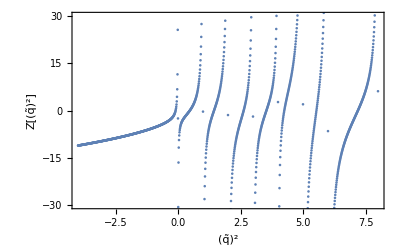

```mathematica
zplot=ListPlot[zdat,Frame->True,PlotRange->{All,{-30,30}},FrameStyle->Directive[Black,18],FrameLabel->{"(q̃)^2","Z[(q̃)^2]"}]
```